# Quantum Noise NIN and NIS for T1 = 3-ΔT/2K, T2 = 3+ΔT/2K as a function of Z for applied voltage bias V = 0.000

```mathematica
T1=3-T/2;
T2=3+T/2;
A=(u0 v0)/(-v0^2 Z^2+u0^2 (1+Z^2));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=-((u0^2-v0^2) Z (ⅈ+Z))/(-v0^2 Z^2+u0^2 (1+Z^2));
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 
Bn=1/(1+Z^2);
kb=8.615*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=100*ds;
ds=1;
a1=kb*T2;
T=1;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.0000;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NS1=NIntegrate[G^2(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS1=NIntegrate[G^2(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN1=NIntegrate[Bn*G^2(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN1=NIntegrate[Bn*G^2(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
list=AppendTo[list1,{Z,(2*Re[Qth11NS]+2*Re[Qsh11NS])/(3*kb),(2*Re[Qth11NN]+2*Re[Qsh11NN])/(3*kb),(2*Re[Qsh11NS]+2*Re[Qth11NS])/(2*Re[Qsh11NN]+2*Re[Qth11NN]),(2*Re[Qth11NS1]+2*Re[Qsh11NS1])/(3^3*kb^3),(2*Re[Qth11NN1]+2*Re[Qsh11NN1])/(3^3*kb^3),(2*Re[Qsh11NS1]+2*Re[Qth11NS1])/(2*Re[Qsh11NN1]+2*Re[Qth11NN1]),2*Re[Qsh11NS]/(3*kb),2*Re[Qsh11NN]/(3*kb),2*Re[Qsh11NS1]/(3*kb)^3,2*Re[Qsh11NN1]/(3*kb)^3}];
},{Z,0.00001,4.0001,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["QT1.dat",listn]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{12.4108,Null}

QT1.dat

```mathematica
Import["QT01.dat"]
```

{{0.00001,8.,4.,2.,26.8673,13.4336,2.,1.90947×10^-11,1.19342×10^-12,8.82009×10^-11,5.51256×10^-12},{0.10001,7.69107,3.96051,1.94194,25.832,13.3011,1.94209,0.00178203,0.000117013,0.00823142,0.0005405},{0.20001,6.86445,3.84658,1.78456,23.061,12.9189,1.78505,0.00583906,0.000441394,0.0269714,0.00203886},{0.30001,5.75502,3.67061,1.56787,19.3399,12.3285,1.56871,0.00966201,0.000904079,0.0446301,0.00417606},{0.40001,4.60293,3.44967,1.33431,15.4732,11.5872,1.33537,0.0116734,0.0014191,0.0539212,0.00655501},{0.50001,3.56725,3.20188,1.11411,11.9951,10.7556,1.11524,0.0117868,0.00190952,0.0544447,0.00882031},{0.60001,2.71477,2.94347,0.922302,9.13078,9.88831,0.923391,0.0106816,0.00232287,0.0493395,0.0107296},{0.70001,2.04962,2.68717,0.762743,6.8949,9.02794,0.763729,0.0090704,0.00263403,0.0418974,0.0121669},{0.80001,1.54631,2.44184,0.633255,5.20249,8.20427,0.634119,0.00741631,0.0028398,0.0342569,0.0131174},{0.90001,1.17134,2.21287,0.529331,3.94134,7.43545,0.530074,0.00594102,0.00295068,0.0274424,0.0136296},{1.00001,0.89358,2.00296,0.446129,3.00695,6.73053,0.446763,0.00471463,0.00298355,0.0217775,0.0137814},{1.10001,0.687686,1.81289,0.379331,2.31424,6.09216,0.379871,0.00373229,0.0029566,0.01724,0.0136569},{1.20001,0.534353,1.64221,0.325386,1.79831,5.51886,0.325848,0.00296025,0.00288652,0.0136738,0.0133332},{1.30001,0.419354,1.48976,0.281491,1.41134,5.00674,0.281887,0.00235855,0.00278723,0.0108945,0.0128746},{1.40001,0.332374,1.35401,0.245474,1.11863,4.55068,0.245817,0.00189056,0.00266971,0.00873276,0.0123317},{1.50001,0.265983,1.2333,0.215668,0.895203,4.14513,0.215965,0.00152587,0.00254218,0.00704822,0.0117427},{1.60001,0.214829,1.126,0.19079,0.723048,3.78459,0.19105,0.00124048,0.00241063,0.00572993,0.011135},{1.70001,0.175045,1.03055,0.169856,0.589154,3.46387,0.170085,0.00101586,0.00227923,0.00469239,0.0105281},{1.80001,0.143819,0.945539,0.152103,0.484059,3.17822,0.152305,0.000837933,0.00215082,0.00387052,0.00993491},{1.90001,0.119092,0.869699,0.136935,0.400839,2.92336,0.137116,0.000696027,0.00202719,0.00321504,0.00936389},{2.00001,0.0993458,0.801903,0.123887,0.334378,2.69552,0.124049,0.000582057,0.00190946,0.0026886,0.00882004},{2.10001,0.0834482,0.741164,0.112591,0.280871,2.4914,0.112736,0.000489886,0.00179818,0.00226285,0.00830605},{2.20001,0.0705507,0.68662,0.102751,0.237461,2.30808,0.102882,0.000414838,0.0016936,0.00191619,0.00782295},{2.30001,0.060011,0.637521,0.0941317,0.201987,2.14307,0.0942513,0.000353328,0.00159568,0.00163207,0.00737064},{2.40001,0.0513384,0.593216,0.0865425,0.172797,1.99416,0.0866515,0.000302592,0.00150425,0.00139772,0.00694832},{2.50001,0.0441556,0.553139,0.0798273,0.148621,1.85946,0.0799271,0.000260489,0.00141904,0.00120323,0.00655473},{2.60001,0.03817,0.5168,0.0738583,0.128475,1.73731,0.0739501,0.000225345,0.00133972,0.0010409,0.00618834},{2.70001,0.033153,0.483772,0.0685302,0.111588,1.6263,0.0686148,0.000195848,0.00126593,0.000904648,0.00584749},{2.80001,0.0289246,0.453683,0.063755,0.097356,1.52516,0.0638332,0.000170959,0.0011973,0.000789681,0.00553048},{2.90001,0.0253422,0.426211,0.0594594,0.0852985,1.43282,0.059532,0.000149852,0.00113346,0.000692186,0.00523562},{3.00001,0.0222923,0.401072,0.0555817,0.0750328,1.34832,0.0556492,0.000131867,0.00107407,0.000609111,0.00496128},{3.10001,0.0196834,0.378019,0.0520698,0.0662517,1.27083,0.0521327,0.000116472,0.00101879,0.000538,0.00470591},{3.20001,0.0174419,0.356837,0.0488792,0.0587073,1.19962,0.0489381,0.000103237,0.000967292,0.000476867,0.00446805},{3.30001,0.015508,0.337335,0.0459722,0.052198,1.13407,0.0460273,0.0000918127,0.000919295,0.000424095,0.00424635},{3.40001,0.0138328,0.319344,0.0433163,0.0465595,1.07359,0.043368,0.0000819117,0.000874519,0.000378362,0.00403952},{3.50001,0.0123761,0.302718,0.0408834,0.0416565,1.0177,0.040932,0.0000732992,0.000832712,0.000338579,0.00384641},{3.60001,0.0111049,0.287325,0.0386493,0.0373778,0.965955,0.0386952,0.0000657807,0.000793642,0.00030385,0.00366594},{3.70001,0.00999175,0.27305,0.0365931,0.033631,0.917967,0.0366364,0.0000591949,0.000757095,0.000273429,0.00349712},{3.80001,0.00901375,0.259789,0.0346964,0.0303392,0.873388,0.0347373,0.0000534073,0.000722875,0.000246696,0.00333906},{3.90001,0.00815182,0.247451,0.0329432,0.027438,0.831912,0.0329819,0.0000483054,0.000690803,0.000223129,0.00319091},{4.00001,0.00738991,0.235954,0.0313193,0.0248736,0.793262,0.0313561,0.0000437947,0.000660713,0.000202294,0.00305192}}

```mathematica
Import["QT1.dat"]
```

{{0.00001,8.,4.,2.,28.5122,14.2561,2.,7.62054×10^-11,4.76284×10^-12,3.48314×10^-10,2.17696×10^-11},{0.10001,7.6964,3.96086,1.94312,27.4373,14.1171,1.94356,0.00711193,0.000466991,0.0325067,0.00213449},{0.20001,6.88191,3.8479,1.78848,24.5508,13.7158,1.78996,0.0233033,0.00176157,0.106513,0.00805165},{0.30001,5.78392,3.67331,1.57458,20.6528,13.0954,1.57711,0.0385603,0.00360811,0.176249,0.0164917},{0.40001,4.63785,3.45392,1.34278,16.5763,12.3155,1.34597,0.0465878,0.00566351,0.21294,0.0258864},{0.50001,3.6025,3.2076,1.12312,12.8868,11.4396,1.1265,0.0470402,0.00762073,0.215008,0.0348323},{0.60001,2.74672,2.95042,0.930958,9.83229,10.5247,0.934211,0.0426293,0.00927038,0.194847,0.0423724},{0.70001,2.07675,2.69505,0.770579,7.43803,9.61581,0.773521,0.0361993,0.0105122,0.165457,0.0480484},{0.80001,1.56849,2.45033,0.640113,5.61994,8.74446,0.642685,0.0295979,0.0113334,0.135284,0.0518019},{0.90001,1.18911,2.2217,0.535226,4.26189,7.93004,0.537437,0.0237102,0.0117759,0.108373,0.0538245},{1.00001,0.907681,2.01189,0.451159,3.25394,7.1824,0.453044,0.0188157,0.0119071,0.0860016,0.0544241},{1.10001,0.698849,1.82174,0.383617,2.50571,6.50459,0.385222,0.0148953,0.0117996,0.0680824,0.0539326},{1.20001,0.543207,1.65085,0.329047,1.9479,5.89526,0.330418,0.0118141,0.0115199,0.0539992,0.0526542},{1.30001,0.426408,1.4981,0.284633,1.52921,5.35046,0.285809,0.0094128,0.0111236,0.0430234,0.0508431},{1.40001,0.338029,1.36199,0.248187,1.21234,4.8649,0.249201,0.00754508,0.0106546,0.0344865,0.0486992},{1.50001,0.270547,1.2409,0.218024,0.970366,4.43282,0.218905,0.00608965,0.0101456,0.0278341,0.046373},{1.60001,0.218539,1.13321,0.19285,0.783864,4.04846,0.19362,0.00495064,0.00962063,0.022628,0.0439733},{1.70001,0.178083,1.03736,0.171669,0.638775,3.70635,0.172346,0.00405421,0.00909625,0.0185307,0.0415765},{1.80001,0.146325,0.951972,0.153707,0.524873,3.40149,0.154307,0.00334412,0.00858375,0.0152851,0.039234},{1.90001,0.121174,0.875762,0.138364,0.434664,3.12938,0.138898,0.00277779,0.00809038,0.0126965,0.0369789},{2.00001,0.101087,0.807614,0.125167,0.362614,2.88603,0.125645,0.00232294,0.0076205,0.0106175,0.0348312},{2.10001,0.0849134,0.746542,0.113742,0.304602,2.66792,0.114172,0.0019551,0.00717642,0.00893623,0.0328014},{2.20001,0.0717915,0.691685,0.103792,0.257534,2.47199,0.104181,0.00165559,0.00675901,0.00756724,0.0308936},{2.30001,0.0610677,0.642294,0.0950776,0.219067,2.29556,0.0954306,0.0014101,0.00636822,0.00644521,0.0291074},{2.40001,0.0522434,0.597715,0.0874052,0.187413,2.13631,0.0877271,0.00120762,0.00600334,0.00551972,0.0274396},{2.50001,0.0449347,0.557384,0.0806172,0.161195,1.99223,0.0809119,0.00103959,0.00566327,0.00475169,0.0258853},{2.60001,0.038844,0.520807,0.0745842,0.139346,1.86155,0.074855,0.000899336,0.00534671,0.00411062,0.0244384},{2.70001,0.0337387,0.487558,0.0691994,0.121033,1.74275,0.069449,0.000781614,0.00505222,0.00357255,0.0230923},{2.80001,0.0294359,0.457264,0.0643739,0.105597,1.63451,0.0646047,0.000682283,0.00477832,0.00311853,0.0218404},{2.90001,0.0257904,0.429601,0.0600335,0.0925198,1.53566,0.0602475,0.000598047,0.00452356,0.00273351,0.020676},{3.00001,0.0226867,0.404284,0.0561156,0.0813857,1.44519,0.0563147,0.00052627,0.00428653,0.00240544,0.0195926},{3.10001,0.0200318,0.381067,0.0525676,0.0718616,1.36222,0.0527532,0.000464831,0.0040659,0.00212462,0.0185841},{3.20001,0.0177507,0.35973,0.0493445,0.0636788,1.28597,0.0495179,0.000412012,0.00386039,0.0018832,0.0176448},{3.30001,0.0157826,0.340084,0.046408,0.0566186,1.21576,0.0465705,0.000366417,0.00366883,0.00167479,0.0167692},{3.40001,0.0140778,0.32196,0.0437253,0.0505027,1.15099,0.0438778,0.000326904,0.00349014,0.00149419,0.0159525},{3.50001,0.0125954,0.305208,0.0412681,0.0451847,1.09112,0.0414115,0.000292532,0.00332329,0.00133708,0.0151899},{3.60001,0.0113017,0.289699,0.0390118,0.0405437,1.03568,0.0391469,0.000262526,0.00316737,0.00119993,0.0144772},{3.70001,0.0101688,0.275314,0.0369352,0.0364797,0.984268,0.0370627,0.000236242,0.00302151,0.0010798,0.0138105},{3.80001,0.00917348,0.261951,0.0350198,0.0329091,0.936504,0.0351404,0.000213144,0.00288494,0.000974225,0.0131863},{3.90001,0.0082963,0.249517,0.0332494,0.0297623,0.89206,0.0333636,0.000192783,0.00275694,0.00088116,0.0126012},{4.00001,0.0075209,0.23793,0.0316097,0.0269806,0.850642,0.031718,0.000174781,0.00263686,0.000798878,0.0120523}}

# Quantum noise correlation for NIN as a function of Z

```mathematica
dataQn0c=Import["QT01.dat"][[All,{1,3}]];
dataQn1c=Import["QT1.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
```

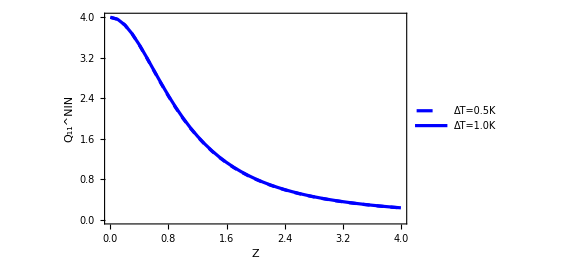

```mathematica
Qn=ListLinePlot[{dataQn0c,dataQn1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",25,Bold,Black],Style["Q_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

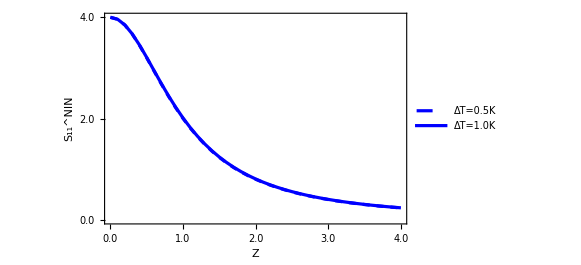

```mathematica
ListLinePlot[{dataQn0c,dataQn1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{2.0,"2.0"}},None},{{{1,"1.0"},{0,"0.0"},{2.0, "2.0"},{3,"3.0"},{4,"4.0"}},None}},FrameLabel->{Style["Z",25,Bold,Black],Style["S_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

# Quantum noise correlation for NIS as a function of Z

```mathematica
dataQs0c=Import["QT1.dat"][[All,{1,2}]];
dataQs1c=Import["QT01.dat"][[All,{1,2}]];
```

```mathematica
Qs=ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{8.0,"8.0"}},None},{{{1,"1.0"},{0,"0.0"},{2.0, "2.0"},{3,"3.0"},{4,"4.0"}},None}},FrameLabel->{Style["Z",25,Bold,Black],Style["Q_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

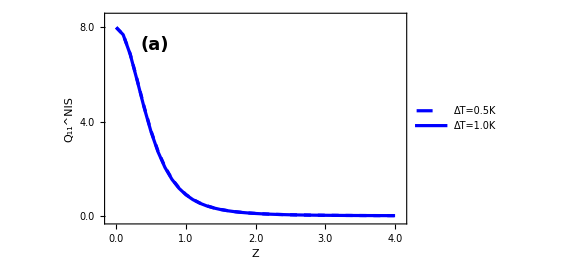

```mathematica
ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{8.0,"8.0"}},None},{{{1,"1.0"},{0,"0.0"},{2.0, "2.0"},{3,"3.0"},{4,"4.0"}},None}},FrameLabel->{Style["Z",25,Bold,Black],Style["S_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

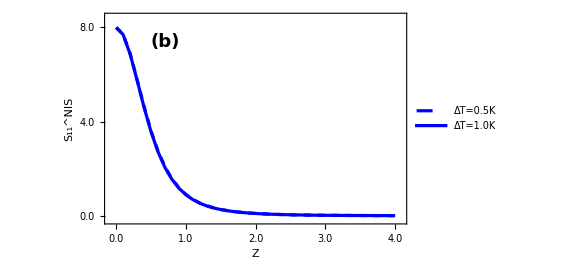

# Ratio of Quantum noise in NIS and NIN as a function of Z

```mathematica
dataQn0=Import["QT1.dat"][[All,{1,4}]];
dataQn1=Import["QT01.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
```

```mathematica
A1=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->{{0,3},{0,2.05}},Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",25,Bold,Black],Style["S_11^NIS/S_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{2.0,"2.0"},{1.0,"1.0"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Black,DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

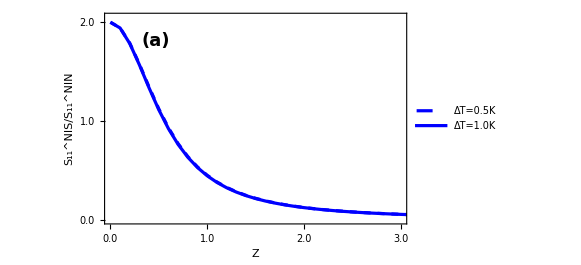

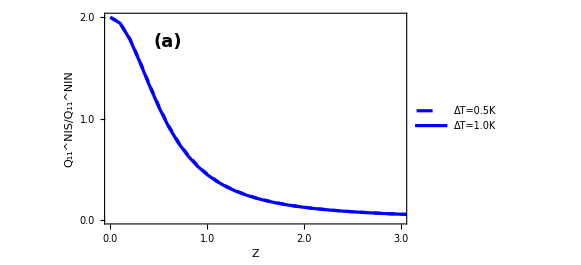

# Quantum heat noise in NIN

```mathematica
dataQn0=Import["QT01.dat"][[All,{1,6}]];
dataQn1=Import["QT1.dat"][[All,{1,6}]];
```

```mathematica
ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^(NIN; H)",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

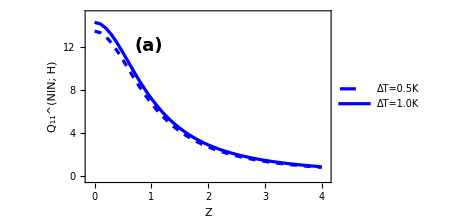

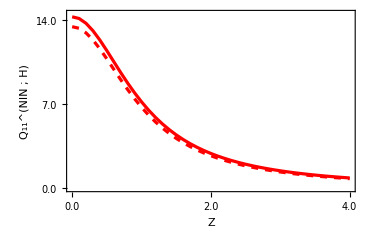

```mathematica
Qhn=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->{0,14.5},FrameTicks->{{{{0.0,"0.0"},{7.0,"7.0"},{14.0,"14.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},FrameLabel->{Style["Z",15,Bold,Black],Style["Q_11^(NIN ;  H)",16,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{dataQn0c,dataQn1c},Frame->True,PlotRange->All,Frame->True,FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{2.0,"2.0"}},None},{{{1,"1.0"},{0,"0.0"},{2.0, "2.0"},{3,"3.0"},{4,"4.0"}},None}},FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qhn,Scaled[{0.5,0.5}],Scaled[{0,0}],2.7],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

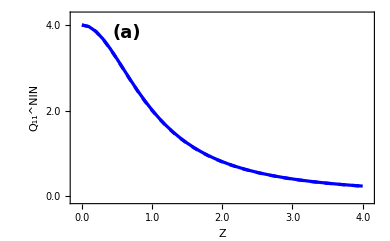

# Quantum heat noise in NIS

```mathematica
dataQn0=Import["QT01.dat"][[All,{1,5}]];
dataQn1=Import["QT1.dat"][[All,{1,5}]];
```

```mathematica
AQn=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^(NIS; H)",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

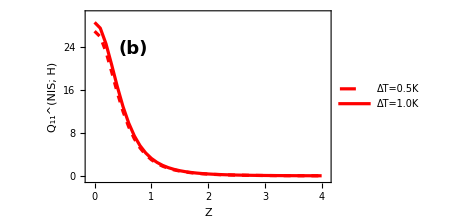

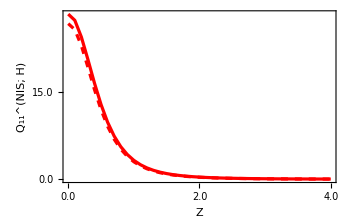

```mathematica
Qhs0=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["Z",16,Bold,Black],Style["Q_11^(NIS; H)",17,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],FrameTicks->{{{{0.0,"0.0"},{15.0,"15.0"},{30.0,"30.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qhs0,Scaled[{0.45,0.45}],Scaled[{0,0}],2.9],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

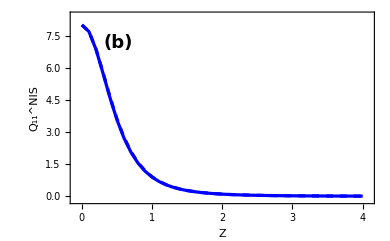

# Quantum charge & heat shot noise in NIN

```mathematica
dataQshn0=Import["QT01.dat"][[All,{1,11}]];
dataQshn1=Import["QT1.dat"][[All,{1,11}]];
```

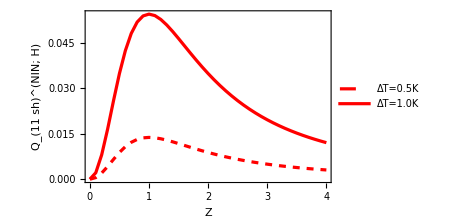

```mathematica
AQn=ListLinePlot[{dataQshn0,dataQshn1},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  sh)^(NIN; H)",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

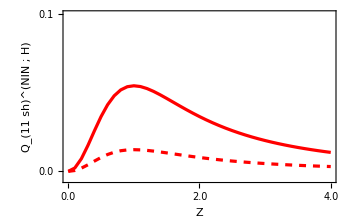

```mathematica
Qshn0=ListLinePlot[{dataQshn0,dataQshn1},Frame->True,PlotRange->{-0.005,0.1},Frame->True,FrameLabel->{Style["Z",16,Bold,Black],Style["Q_(11  sh)^(NIN ; H)",17,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],FrameTicks->{{{{0.0,"0.0"},{0.1,"0.1"},{0.2,"0.2"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
dataQsh0nc=Import["QT1.dat"][[All,{1,9}]];
dataQsh1nc=Import["QT01.dat"][[All,{1,9}]];
```

```mathematica
DTn=ListLinePlot[{dataQsh0nc,dataQsh1nc},Frame->True,PlotRange->{0,0.02},Frame->True,FrameLabel->{Style["Z",20,Bold,Black],Style["Δ_T^NIN",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,11],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.01,"0.01"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

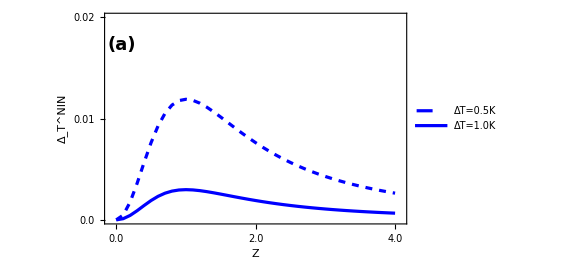

```mathematica
ListLinePlot[{dataQsh0nc,dataQsh1nc},Frame->True,PlotRange->{0,0.02},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  sh)^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.01,"0.01"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qshn0,Scaled[{0.49,0.5}],Scaled[{0,0}],2.75],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

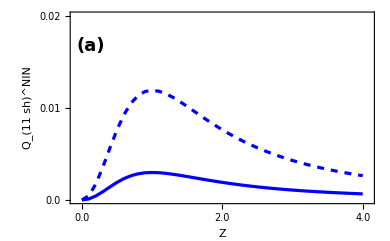

```mathematica
dataQn0c=Import["QT01.dat"][[All,{1,3}]];
dataQn1c=Import["QT1.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
```

```mathematica
ListLinePlot[{dataQn0c,dataQn1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Left,Bottom}],FrameLabel->{Style["Z",25,Bold,Black],Style["S_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[DTn,Scaled[{0.48,0.45}],Scaled[{0,0}],2.75],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

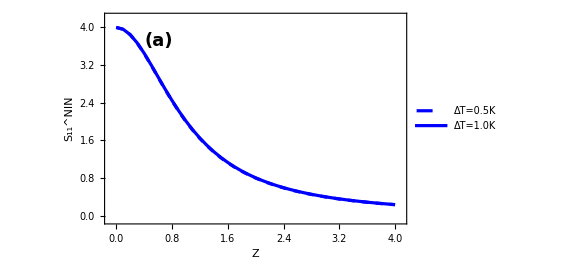

# Quantum charge & heat shot noise in NIS

```mathematica
dataQshs0=Import["QT01.dat"][[All,{1,10}]];
dataQshs1=Import["QT1.dat"][[All,{1,10}]];
```

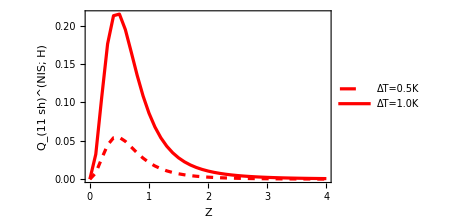

```mathematica
AQn=ListLinePlot[{dataQshs0,dataQshs1},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  sh)^(NIS; H)",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

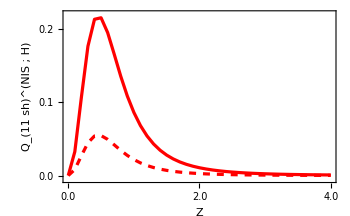

```mathematica
Qshs0=ListLinePlot[{dataQshs0,dataQshs1},Frame->True,PlotRange->{-0.005,0.22},Frame->True,FrameLabel->{Style["Z",16,Bold,Black],Style["Q_(11  sh)^(NIS ; H)",17,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],FrameTicks->{{{{0.0,"0.0"},{0.1,"0.1"},{0.2,"0.2"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
dataQsh0c=Import["QT1.dat"][[All,{1,8}]];
dataQsh1c=Import["QT01.dat"][[All,{1,8}]];
```

```mathematica
DTs=ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{-0.001,0.06},Frame->True,FrameLabel->{Style["Z",20,Bold,Black],Style["Δ_T^NIS",20,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.04,"0.04"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

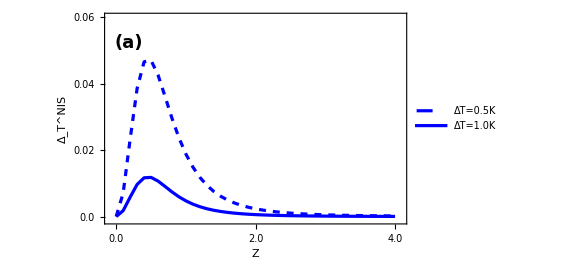

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{0,0.06},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  sh)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.04,"0.04"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qshs0,Scaled[{0.42,0.4}],Scaled[{0,0}],3],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

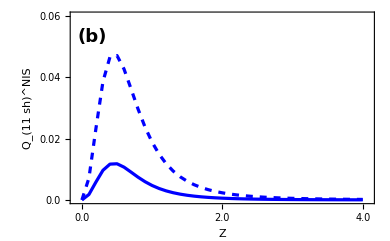

```mathematica
dataQs0c=Import["QT01.dat"][[All,{1,2}]];
dataQs1c=Import["QT1.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
```

```mathematica
ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",15,Black,Bold],Style["ΔT=1.0K",15,Black,Bold]},{Left,Bottom}],FrameLabel->{Style["Z",25,Bold,Black],Style["S_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[DTs,Scaled[{0.48,0.45}],Scaled[{0,0}],2.75],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

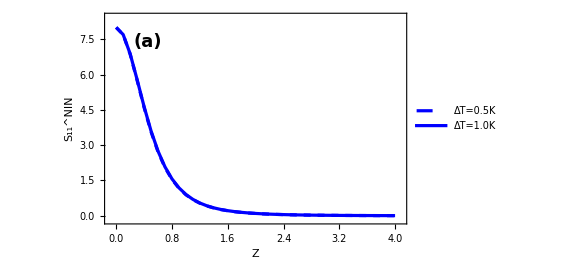

# Ratio of quantum heat noise in NIS and NIN

```mathematica
dataQn0=Import["QT01.dat"][[All,{1,7}]];
dataQn1=Import["QT1.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
AQn=ListLinePlot[{dataQn0,dataQn1},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^(NIS; H)/Q_11^(NIN; H)",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Magenta,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],RGBColor[0,.6,.7]],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15]]
```

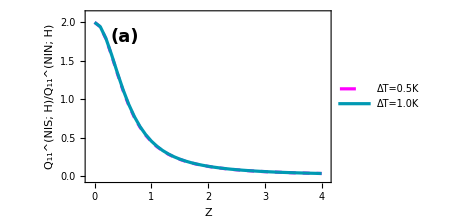

# Ratio of charge shot noise in NIS/NIN

```mathematica
dataQsh0nc=Import["QT1.dat"][[All,{1,9}]];
dataQsh1nc=Import["QT01.dat"][[All,{1,9}]];
```

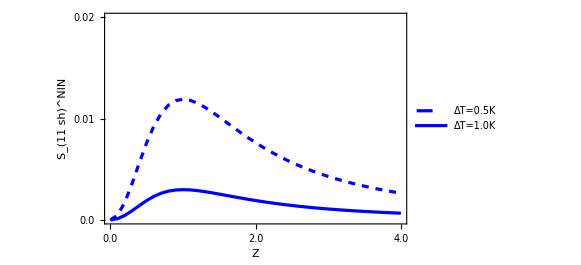

```mathematica
ListLinePlot[{dataQsh0nc,dataQsh1nc},Frame->True,PlotRange->{0,0.02},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Style["S_(11  sh)^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.01,"0.01"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
dataQsh0c=Import["QT1.dat"][[All,{1,8}]];
dataQsh1c=Import["QT01.dat"][[All,{1,8}]];
```

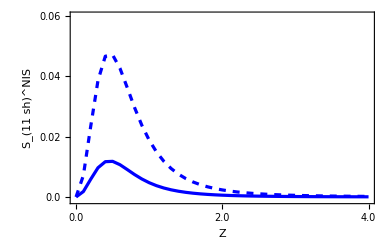

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{-0.001,0.06},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["S_(11  sh)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.04,"0.04"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
Rshncz=Table[Flatten[{Import["QT1.dat"][[x]][[1]],Import["QT1.dat"][[x]][[8]]/Import["QT1.dat"][[x]][[9]]}],{x,1,41,1}]
```

{{0.00001,16.},{0.10001,15.2293},{0.20001,13.2287},{0.30001,10.6871},{0.40001,8.22595},{0.50001,6.17266},{0.60001,4.59844},{0.70001,3.44355},{0.80001,2.61156},{0.90001,2.01344},{1.00001,1.58021},{1.10001,1.26236},{1.20001,1.02554},{1.30001,0.846199},{1.40001,0.708153},{1.50001,0.600223},{1.60001,0.514586},{1.70001,0.445702},{1.80001,0.389588},{1.90001,0.343345},{2.00001,0.304828},{2.10001,0.272434},{2.20001,0.244945},{2.30001,0.221429},{2.40001,0.201159},{2.50001,0.183567},{2.60001,0.168204},{2.70001,0.154707},{2.80001,0.142787},{2.90001,0.132207},{3.00001,0.122773},{3.10001,0.114324},{3.20001,0.106728},{3.30001,0.099873},{3.40001,0.0936649},{3.50001,0.0880247},{3.60001,0.0828845},{3.70001,0.0781868},{3.80001,0.0738818},{3.90001,0.0699265},{4.00001,0.066284}}

```mathematica
Rshncz1=Table[Flatten[{Import["QT01.dat"][[x]][[1]],Import["QT01.dat"][[x]][[8]]/Import["QT01.dat"][[x]][[9]]}],{x,1,41,1}]
```

{{0.00001,16.},{0.10001,15.2293},{0.20001,13.2287},{0.30001,10.6871},{0.40001,8.22595},{0.50001,6.17266},{0.60001,4.59844},{0.70001,3.44355},{0.80001,2.61156},{0.90001,2.01344},{1.00001,1.58021},{1.10001,1.26236},{1.20001,1.02554},{1.30001,0.846199},{1.40001,0.708153},{1.50001,0.600223},{1.60001,0.514586},{1.70001,0.445702},{1.80001,0.389588},{1.90001,0.343345},{2.00001,0.304828},{2.10001,0.272434},{2.20001,0.244945},{2.30001,0.221429},{2.40001,0.201159},{2.50001,0.183567},{2.60001,0.168204},{2.70001,0.154707},{2.80001,0.142787},{2.90001,0.132207},{3.00001,0.122773},{3.10001,0.114324},{3.20001,0.106728},{3.30001,0.099873},{3.40001,0.0936649},{3.50001,0.0880247},{3.60001,0.0828845},{3.70001,0.0781868},{3.80001,0.0738818},{3.90001,0.0699265},{4.00001,0.066284}}

```mathematica
ListLinePlot[{Rshncz,Rshncz1},Frame->True,PlotRange->{0,16.5},Frame->True,FrameLabel->{Style["Z",22,Bold,Black],Rotate[Style["Δ_T^NIS/Δ_T^NIN",22,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{20.06,"0.06"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

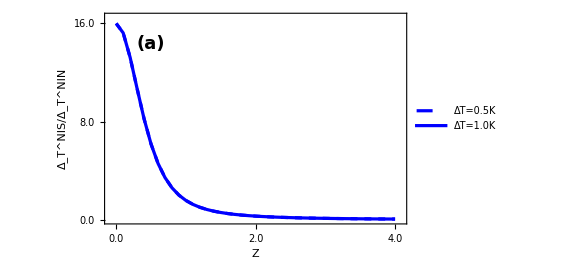

# Ratio of Heat shot noise in NIS/NIN

```mathematica
dataQsh0nh=Import["QT1.dat"][[All,{1,11}]];
dataQsh1nh=Import["QT01.dat"][[All,{1,11}]];
```

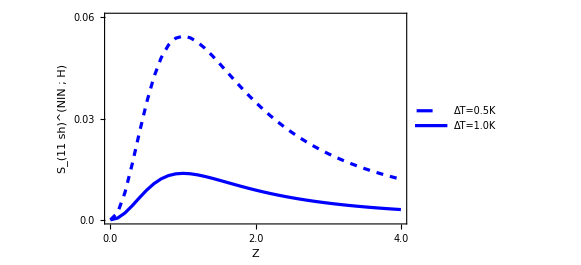

```mathematica
ListLinePlot[{dataQsh0nh,dataQsh1nh},Frame->True,PlotRange->{0,0.06},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Style["S_(11  sh)^(NIN ;  H)",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{0.06,"0.06"},{0.08,"0.08"},{0.03,"0.03"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
dataQsh0h=Import["QT1.dat"][[All,{1,10}]];
dataQsh1h=Import["QT01.dat"][[All,{1,10}]];
```

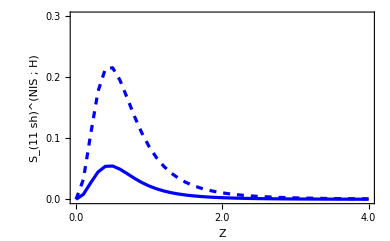

```mathematica
ListLinePlot[{dataQsh0h,dataQsh1h},Frame->True,PlotRange->{-0.001,0.3},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Style["S_(11  sh)^(NIS ;  H)",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.3,"0.3"},{0.1,"0.1"},{0.2,"0.2"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
Rshnhz=Table[Flatten[{Import["QT1.dat"][[x]][[1]],Import["QT1.dat"][[x]][[10]]/Import["QT1.dat"][[x]][[11]]}],{x,1,41,1}]
```

{{0.00001,16.},{0.10001,15.2293},{0.20001,13.2287},{0.30001,10.6871},{0.40001,8.22595},{0.50001,6.17266},{0.60001,4.59844},{0.70001,3.44355},{0.80001,2.61156},{0.90001,2.01345},{1.00001,1.58021},{1.10001,1.26236},{1.20001,1.02554},{1.30001,0.846199},{1.40001,0.708154},{1.50001,0.600223},{1.60001,0.514586},{1.70001,0.445702},{1.80001,0.389588},{1.90001,0.343345},{2.00001,0.304828},{2.10001,0.272434},{2.20001,0.244945},{2.30001,0.221429},{2.40001,0.201159},{2.50001,0.183567},{2.60001,0.168204},{2.70001,0.154707},{2.80001,0.142787},{2.90001,0.132207},{3.00001,0.122773},{3.10001,0.114324},{3.20001,0.106728},{3.30001,0.099873},{3.40001,0.093665},{3.50001,0.0880247},{3.60001,0.0828846},{3.70001,0.0781868},{3.80001,0.0738818},{3.90001,0.0699266},{4.00001,0.066284}}

```mathematica
Rshnhz1=Table[Flatten[{Import["QT01.dat"][[x]][[1]],Import["QT01.dat"][[x]][[10]]/Import["QT01.dat"][[x]][[11]]}],{x,1,41,1}]
```

{{0.00001,16.},{0.10001,15.2293},{0.20001,13.2287},{0.30001,10.6871},{0.40001,8.22595},{0.50001,6.17266},{0.60001,4.59844},{0.70001,3.44355},{0.80001,2.61156},{0.90001,2.01345},{1.00001,1.58021},{1.10001,1.26236},{1.20001,1.02554},{1.30001,0.846199},{1.40001,0.708154},{1.50001,0.600223},{1.60001,0.514586},{1.70001,0.445702},{1.80001,0.389588},{1.90001,0.343345},{2.00001,0.304828},{2.10001,0.272434},{2.20001,0.244945},{2.30001,0.221429},{2.40001,0.201159},{2.50001,0.183567},{2.60001,0.168204},{2.70001,0.154707},{2.80001,0.142787},{2.90001,0.132207},{3.00001,0.122773},{3.10001,0.114324},{3.20001,0.106728},{3.30001,0.099873},{3.40001,0.093665},{3.50001,0.0880247},{3.60001,0.0828846},{3.70001,0.0781868},{3.80001,0.0738818},{3.90001,0.0699266},{4.00001,0.066284}}

```mathematica
ListLinePlot[{Rshnhz,Rshnhz1},Frame->True,PlotRange->{0,16.5},Frame->True,FrameLabel->{Style["Z",24,Bold,Black],Style["Q_(11  sh)^(NIS ;  H)/Q_(11  sh)^(NIN ;  H)",24,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.0"},{20.06,"0.06"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red, DotDashed]},ImageSize->390,LabelStyle->Directive[Bold,Black,15]]
```

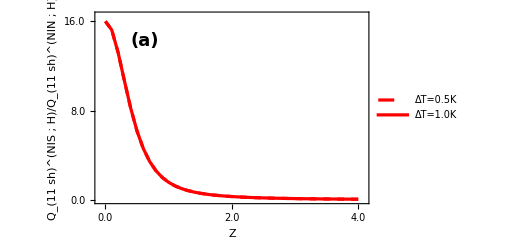

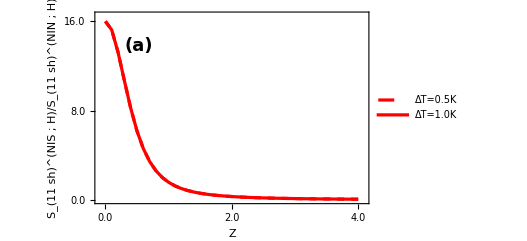

# Quantum Noise NIN and NIS for Z = 0, 1, 3, T2 = 3K as a function of ΔT for applied voltage bias V = 0.0001

```mathematica
T1=3-T/2;
T2=3+T/2;
A=(u0 v0)/(-v0^2 Z^2+u0^2 (1+Z^2));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=-((u0^2-v0^2) Z (ⅈ+Z))/(-v0^2 Z^2+u0^2 (1+Z^2));
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 
Bn=1/(1+Z^2);
kb=8.615*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=100*ds;
ds=1;
a1=kb*T2;
Z=0.05;  (* 0.01, 1, 3*)
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.0000;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NS1=NIntegrate[G^2(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS1=NIntegrate[G^2(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN1=NIntegrate[Bn*G^2(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN1=NIntegrate[Bn*G^2(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
list=AppendTo[list1,{T,(2*Re[Qth11NS]+2*Re[Qsh11NS])/(3*kb),(2*Re[Qth11NN]+2*Re[Qsh11NN])/(3*kb),(2*Re[Qsh11NS]+2*Re[Qth11NS])/(2*Re[Qsh11NN]+2*Re[Qth11NN]),(2*Re[Qth11NS1]+2*Re[Qsh11NS1])/(3^3*kb^3),(2*Re[Qth11NN1]+2*Re[Qsh11NN1])/(3^3*kb^3),(2*Re[Qsh11NS1]+2*Re[Qth11NS1])/(2*Re[Qsh11NN1]+2*Re[Qth11NN1]),2*Re[Qsh11NS]/(3*kb),2*Re[Qsh11NN]/(3*kb),2*Re[Qsh11NS1]/(3*kb)^3,2*Re[Qsh11NN1]/(3*kb)^3}];
},{T,0.001,1.01,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["check300.dat",listn]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{9.47727,Null}

check300.dat

```mathematica
Import["check300.dat"]
```

{{0.001,7.9206,3.99002,1.9851,26.0577,13.1267,1.9851,1.87785×10^-9,1.18837×10^-10,8.70475×10^-9,5.50868×10^-10},{0.101,7.92062,3.99003,1.9851,26.08,13.1378,1.98511,0.0000191554,1.21222×10^-6,0.0000887816,5.61842×10^-6},{0.201,7.92067,3.99003,1.98512,26.1458,13.1709,1.98512,0.0000758578,4.80056×10^-6,0.000351437,0.0000222402},{0.301,7.92077,3.99004,1.98514,26.2552,13.2258,1.98515,0.000170089,0.0000107638,0.000787433,0.0000498316},{0.401,7.9209,3.99004,1.98517,26.4083,13.3026,1.98519,0.000301814,0.0000190999,0.00139587,0.000088336},{0.501,7.92107,3.99005,1.9852,26.6049,13.4014,1.98524,0.000470985,0.0000298056,0.00217551,0.000137674},{0.601,7.92127,3.99007,1.98525,26.8452,13.522,1.9853,0.000677541,0.0000428772,0.00312475,0.000197745},{0.701,7.92152,3.99008,1.9853,27.129,13.6645,1.98537,0.000921406,0.0000583099,0.00424165,0.000268427},{0.801,7.9218,3.9901,1.98536,27.4565,13.8288,1.98545,0.00120249,0.0000760981,0.00552394,0.000349575},{0.901,7.92212,3.99012,1.98543,27.8275,14.0151,1.98553,0.0015207,0.0000962353,0.00696904,0.000441026},{1.001,7.92247,3.99014,1.98551,28.2421,14.2233,1.98563,0.00187591,0.000118714,0.00857402,0.000542595}}

```mathematica
Import["check301.dat"]
```

{{0.001,0.888889,2.,0.444445,2.92433,6.57974,0.444445,1.88732×10^-8,1.19432×10^-8,8.74866×10^-8,5.53626×10^-8},{0.101,0.889082,2.00012,0.444514,2.92771,6.58589,0.444542,0.00019252,0.000121829,0.000892294,0.000564655},{0.201,0.889651,2.00048,0.444718,2.93771,6.60412,0.444829,0.000762405,0.000482459,0.00353209,0.00223515},{0.301,0.890599,2.00108,0.445059,2.95432,6.63442,0.445302,0.00170947,0.00108177,0.00791405,0.00500811},{0.401,0.891922,2.00192,0.445534,2.97755,6.67678,0.445955,0.00303336,0.00191955,0.0140292,0.00887782},{0.501,0.893623,2.003,0.446143,3.00736,6.7312,0.44678,0.0047336,0.00299548,0.0218648,0.0138363},{0.601,0.895699,2.00431,0.446886,3.04376,6.79766,0.447765,0.00680958,0.00430919,0.0314051,0.0198735},{0.701,0.89815,2.00586,0.447763,3.08671,6.87615,0.448901,0.00926054,0.00586018,0.0426304,0.0269771},{0.801,0.900975,2.00765,0.448771,3.1362,6.96667,0.450173,0.0120856,0.00764791,0.0555181,0.0351325},{0.901,0.904173,2.00967,0.449911,3.1922,7.06918,0.451566,0.0152837,0.00967171,0.0700419,0.0443234},{1.001,0.907743,2.01193,0.45118,3.25468,7.18368,0.453067,0.0188537,0.0119309,0.0861727,0.0545312}}

```mathematica
Import["check302.dat"]
```

{{0.001,0.0221607,0.4,0.0554017,0.0729057,1.31595,0.0554017,5.27873×10^-10,4.29956×10^-9,2.44695×10^-9,1.99305×10^-8},{0.101,0.0221661,0.400044,0.0554091,0.0729927,1.31727,0.0554121,5.38467×10^-6,0.0000438585,0.0000249569,0.000203276},{0.201,0.022182,0.400174,0.0554309,0.07325,1.32118,0.0554427,0.000021324,0.000173685,0.0000987905,0.000804655},{0.301,0.0222085,0.400389,0.0554672,0.0736775,1.32769,0.0554932,0.0000478127,0.000389438,0.000221351,0.00180292},{0.401,0.0222455,0.400691,0.0555179,0.0742751,1.33678,0.0555628,0.0000848412,0.000691037,0.000392387,0.00319601},{0.501,0.0222931,0.401078,0.0555828,0.0750422,1.34845,0.0556506,0.000132396,0.00107837,0.000611547,0.00498108},{0.601,0.0223511,0.401551,0.055662,0.0759786,1.36271,0.0557554,0.00019046,0.00155131,0.000878382,0.00715447},{0.701,0.0224197,0.40211,0.0557551,0.0770836,1.37955,0.055876,0.000259012,0.00210967,0.00119235,0.00971174},{0.801,0.0224987,0.402753,0.0558622,0.0783566,1.39895,0.0560108,0.000338027,0.00275325,0.00155281,0.0126477},{0.901,0.0225881,0.403482,0.0559831,0.0797969,1.42093,0.0561583,0.000427476,0.00348182,0.00195903,0.0159564},{1.001,0.022688,0.404295,0.0561174,0.0814036,1.44546,0.0563167,0.000527327,0.00429511,0.0024102,0.0196312}}

# Quantum noise in NIN setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

```mathematica
data1cn=Import["check300.dat"][[All,{1,3}]];
data2cn=Import["check301.dat"][[All,{1,3}]];
data3cn=Import["check302.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{2.00,"2.0"},{4,"4.0"},{7,"7.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

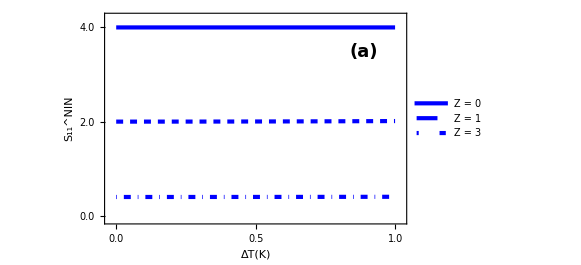

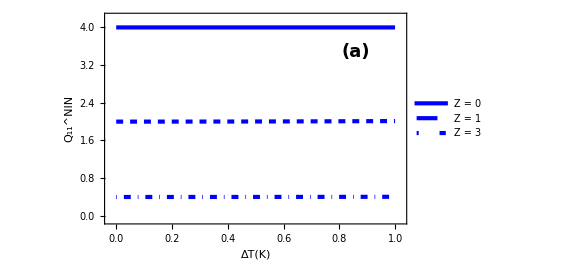

# Quantum noise in NIS setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

```mathematica
data1cs=Import["check300.dat"][[All,{1,2}]];
data2cs=Import["check301.dat"][[All,{1,2}]];
data3cs=Import["check302.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
```

```mathematica
A1=ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.0002,"0.2"},{4,"4.0"},{8,"8.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

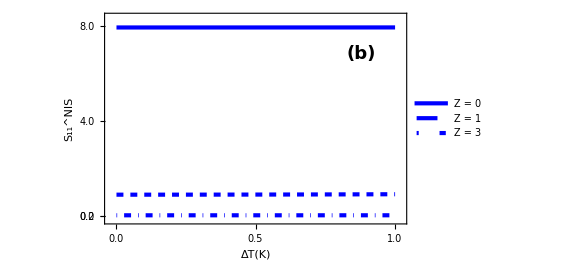

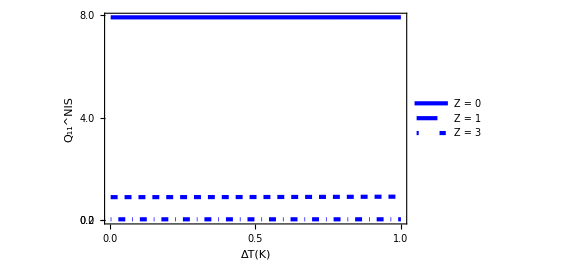

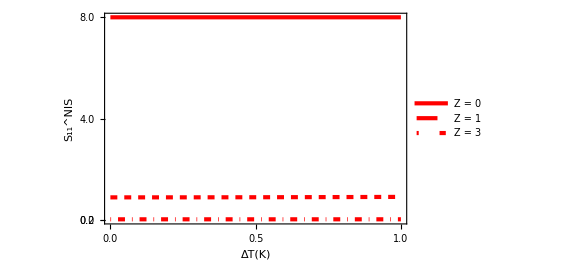

```mathematica
ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.0002,"0.2"},{4,"4.0"},{8,"8.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

# Ratio of quantum noise in NIS and NIN for different Z as a function of ΔT

```mathematica
data1=Import["check300.dat"][[All,{1,4}]];
data2=Import["check301.dat"][[All,{1,4}]];
data3=Import["check302.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
```

```mathematica
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_11^NIS/S_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue,DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

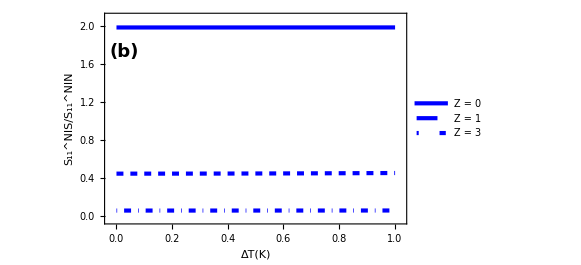

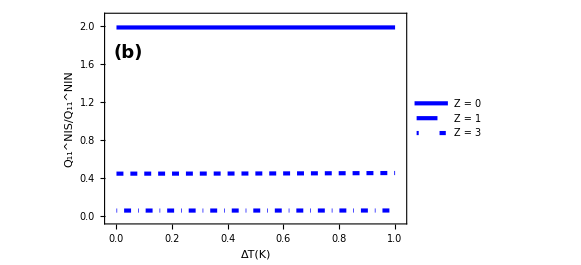

# Quantum heat noise in NIN

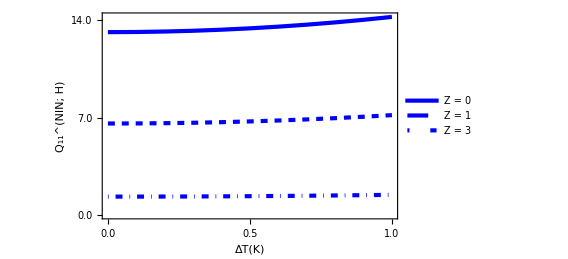

```mathematica
data1=Import["check300.dat"][[All,{1,6}]];
data2=Import["check301.dat"][[All,{1,6}]];
data3=Import["check302.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^(NIN; H)",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{80.00,"80.0"},{14,"14.0"},{7,"7.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->420,LabelStyle->Directive[Bold,Black,15]]
```

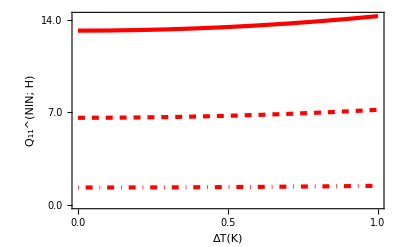

```mathematica
Qhn0=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,FrameTicks->{{{{0.0,"0.0"},{80.00,"80.0"},{14,"14.0"},{7,"7.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},FrameLabel->{Style["ΔT(K)",15,Bold,Black],Style["Q_11^(NIN; H)",16,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->400,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qhn0,Scaled[{0.18,0.5}],Scaled[{0,0}],.62],PlotRange->{0.2,0.3},PlotRangeClipping->False}
]
```

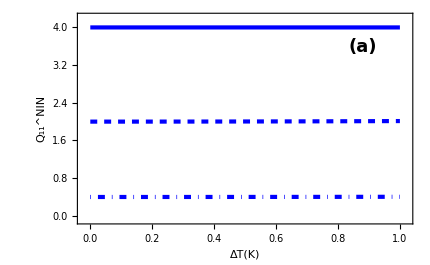

# Quantum heat noise NIS

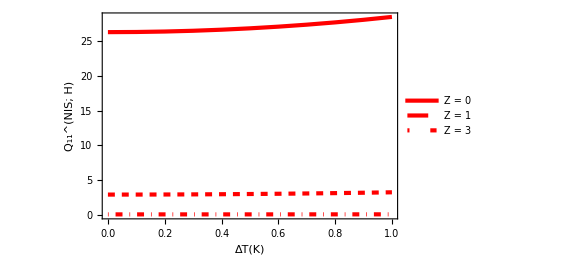

```mathematica
data1=Import["check300.dat"][[All,{1,5}]];
data2=Import["check301.dat"][[All,{1,5}]];
data3=Import["check302.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^(NIS; H)",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->420,LabelStyle->Directive[Bold,Black,15]]
```

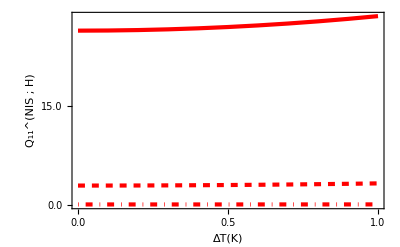

```mathematica
Qsh0=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,FrameTicks->{{{{0.0,"0.0"},{15.00,"15.0"},{30,"30.0"},{120,"120.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},FrameLabel->{Style["ΔT(K)",15,Bold,Black],Style["Q_11^(NIS ; H)",17,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->400,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.0002,"0.2"},{4,"4.0"},{8,"8.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qsh0,Scaled[{0.21,0.4}],Scaled[{0,0}],.69],PlotRange->{0.2,0.3},PlotRangeClipping->False}
]
```

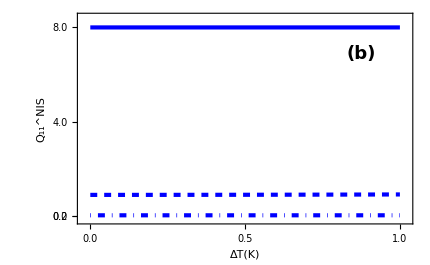

# Ratio of quantum heat noise in NIS and NIN

```mathematica
data1=Import["check300.dat"][[All,{1,7}]];
data2=Import["check301.dat"][[All,{1,7}]];
data3=Import["check302.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Center,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_11^(NIS; H)/Q_11^(NIN; H)",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Black, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Black, DotDashed]},ImageSize->420,LabelStyle->Directive[Bold,Black,15]]
```

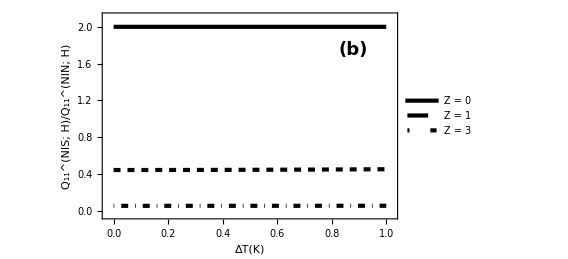

# Quantum charge and heat shot noise NIN

```mathematica
data1hn=Import["check300.dat"][[All,{1,11}]];
data2hn=Import["check301.dat"][[All,{1,11}]];
data3hn=Import["check302.dat"][[All,{1,11}]];
Needs["PlotLegends`"]
```

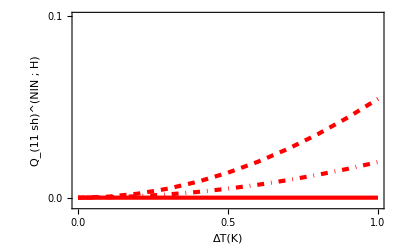

```mathematica
Qsh0hn=ListLinePlot[{data1hn,data2hn,data3hn},Frame->True,PlotRange->{-0.004,.1},Frame->True,FrameTicks->{{{{0.0,"0.0"},{60.00,"60.0"},{.1,"0.1"},{1.,"1.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},FrameLabel->{Style["ΔT(K)",15,Bold,Black],Style["Q_(11  sh)^(NIN ;  H)",17,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->400,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{70,8},{65,35}},PlotRangeClipping->False,Epilog->{Text[Style["",Black,12,Bold],Scaled[{0.12,1.1}]]}]
```

```mathematica
data1cn=Import["check300.dat"][[All,{1,9}]];
data2cn=Import["check301.dat"][[All,{1,9}]];
data3cn=Import["check302.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.001,0.02},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Right,Top}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Δ_T^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.02,"0.02"},{0.01,"0.01"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

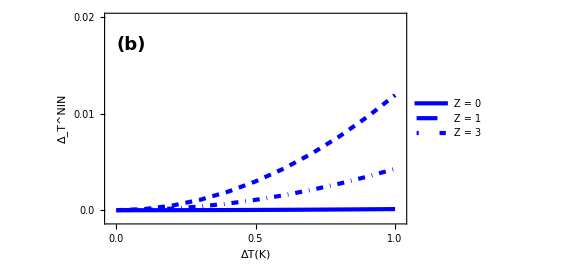

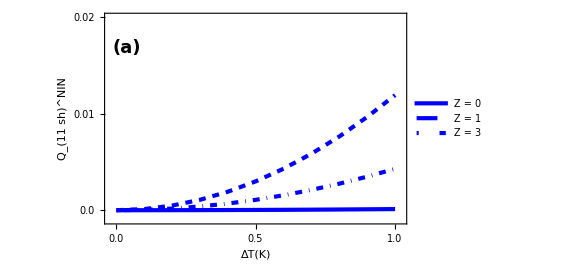

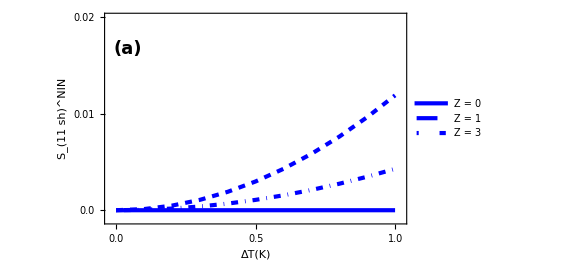

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.001,0.02},Frame->True,FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_(11  sh)^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.02,"0.02"},{0.01,"0.01"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qsh0hn,Scaled[{0.18,0.45}],Scaled[{0,0}],.7],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{88,10},{70,35}},PlotRangeClipping->False]
```

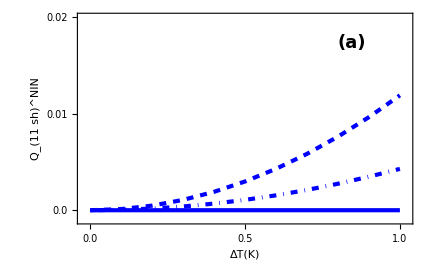

# Quantum charge and heat shot noise NIS

```mathematica
data1h=Import["check300.dat"][[All,{1,10}]];
data2h=Import["check301.dat"][[All,{1,10}]];
data3h=Import["check302.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
```

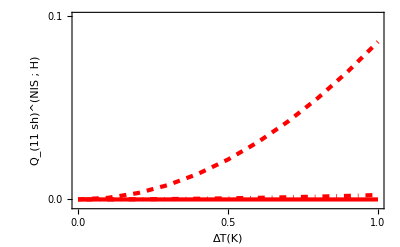

```mathematica
Qsh0h=ListLinePlot[{data1h,data2h,data3h},Frame->True,PlotRange->{-0.003,.1},Frame->True,FrameTicks->{{{{0.0,"0.0"},{60.00,"60.0"},{.1,"0.1"},{1.1,"1.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},FrameLabel->{Style["ΔT(K)",15,Bold,Black],Style["Q_(11  sh)^(NIS ;  H)",17,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->400,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{70,8},{65,35}},PlotRangeClipping->False,Epilog->{Text[Style["",Black,12,Bold],Scaled[{0.12,1.1}]]}]
```

```mathematica
data1cs=Import["check300.dat"][[All,{1,8}]];
data2cs=Import["check301.dat"][[All,{1,8}]];
data3cs=Import["check302.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
```

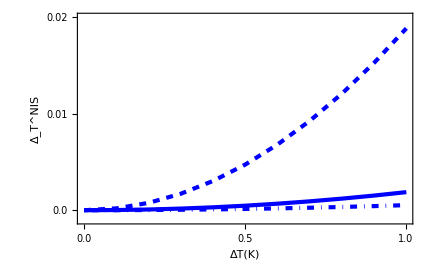

```mathematica
DTTs=ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->{-0.001,0.02},Frame->True,FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_T^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,10],FrameTicks->{{{{0.0,"0.0"},{0.01,"0.01"},{0.02,"0.02"},{1.05,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->{-0.001,0.02},Frame->True,FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["Q_(11  sh)^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.01,"0.01"},{0.02,"0.02"},{1.05,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qsh0h,Scaled[{0.19,0.49}],Scaled[{0,0}],.7],PlotRange->{0.2,0.3},PlotRangeClipping->False},ImagePadding->{{89,10},{70,35}},PlotRangeClipping->False]
```

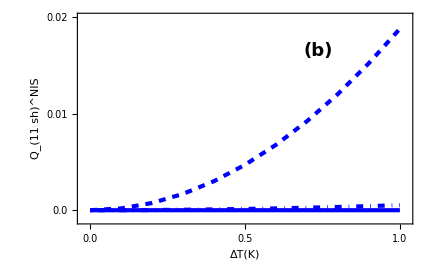

```mathematica
data1cs=Import["check300.dat"][[All,{1,2}]];
data2cs=Import["check301.dat"][[All,{1,2}]];
data3cs=Import["check302.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
```

```mathematica
ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Left,Center}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_11^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{4,"4.0"},{8,"8.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[DTTs,Scaled[{0.51,0.45}],Scaled[{0,0}],.67],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

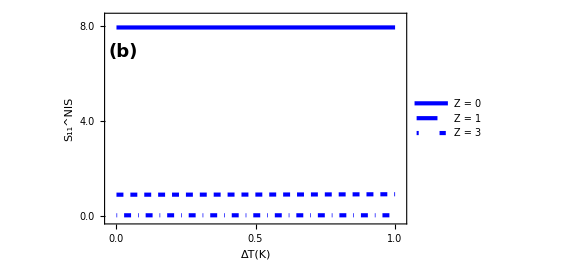

# Ratio of charge shot noise in NIS/NIN

```mathematica
data1cs=Import["check300.dat"][[All,{1,8}]];
data2cs=Import["check301.dat"][[All,{1,8}]];
data3cs=Import["check302.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

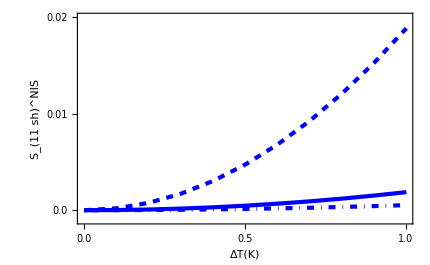

```mathematica
ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->{-0.001,0.02},Frame->True,FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_(11  sh)^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.01,"0.01"},{0.02,"0.02"},{1.05,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
data1cn=Import["check300.dat"][[All,{1,9}]];
data2cn=Import["check301.dat"][[All,{1,9}]];
data3cn=Import["check302.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
```

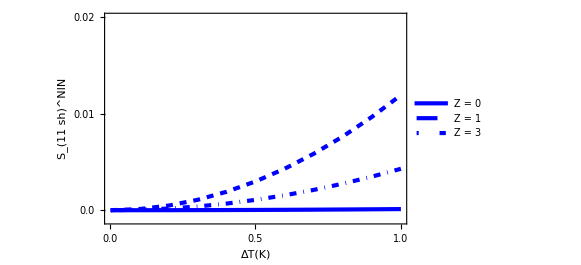

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.001,0.02},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Right,Top}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_(11  sh)^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.02,"0.02"},{0.01,"0.01"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
Rshnc=Table[Flatten[{Import["check300.dat"][[x]][[1]],Import["check300.dat"][[x]][[8]]/Import["check300.dat"][[x]][[9]]}],{x,1,11,1}]
```

{{0.001,15.8019},{0.101,15.8019},{0.201,15.8019},{0.301,15.8019},{0.401,15.8019},{0.501,15.8019},{0.601,15.8019},{0.701,15.8019},{0.801,15.8019},{0.901,15.8019},{1.001,15.8019}}

```mathematica
Rshnc1=Table[Flatten[{Import["check301.dat"][[x]][[1]],Import["check301.dat"][[x]][[8]]/Import["check301.dat"][[x]][[9]]}],{x,1,11,1}]
Rshnc2=Table[Flatten[{Import["check302.dat"][[x]][[1]],Import["check302.dat"][[x]][[8]]/Import["check302.dat"][[x]][[9]]}],{x,1,11,1}]
```

{{0.001,1.58025},{0.101,1.58025},{0.201,1.58025},{0.301,1.58025},{0.401,1.58025},{0.501,1.58025},{0.601,1.58025},{0.701,1.58025},{0.801,1.58025},{0.901,1.58025},{1.001,1.58025}}

{{0.001,0.122774},{0.101,0.122774},{0.201,0.122774},{0.301,0.122774},{0.401,0.122774},{0.501,0.122774},{0.601,0.122774},{0.701,0.122774},{0.801,0.122774},{0.901,0.122774},{1.001,0.122774}}

```mathematica
ListLinePlot[{Rshnc,Rshnc1,Rshnc2},Frame->True,PlotRange->{-0.2,16.15},Frame->True,PlotLegends->Placed[{"Z=0.05","Z = 1","Z = 3"},{Right,Top}],FrameLabel->{Style["ΔT(K)",21,Bold,Black],Rotate[Style["Δ_T^NIS/Δ_T^NIN",22,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{20,"20.0"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,16]]
```

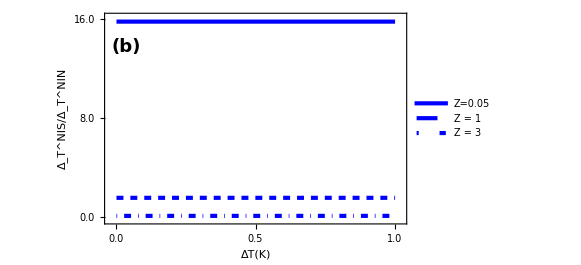

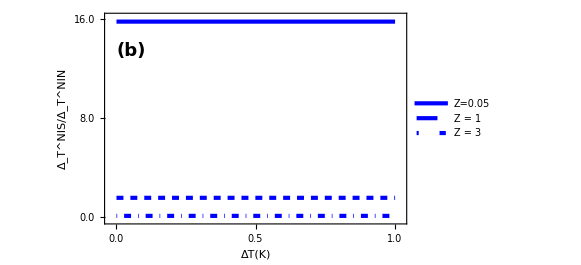

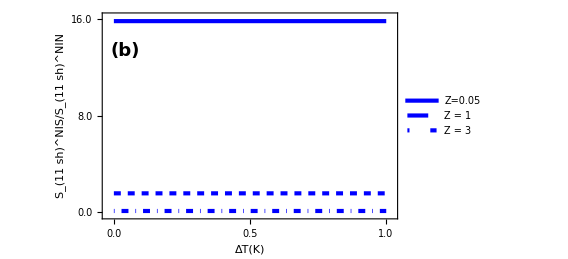

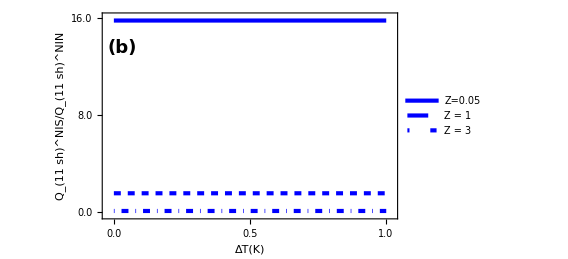

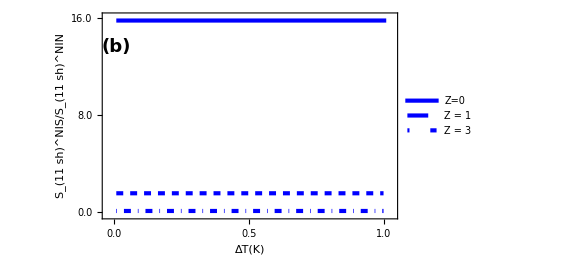

# Ratio of Heat shot noise in NIS/NIN

```mathematica
data1hs=Import["check300.dat"][[All,{1,10}]];
data2hs=Import["check301.dat"][[All,{1,10}]];
data3hs=Import["check302.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

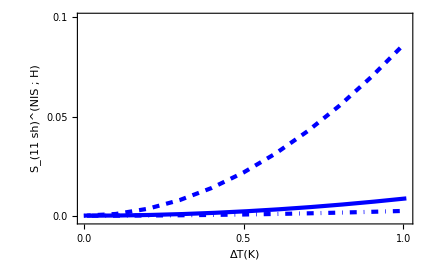

```mathematica
ListLinePlot[{data1hs,data2hs,data3hs},Frame->True,PlotRange->{-0.0021,0.1},Frame->True,FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_(11  sh)^(NIS ;  H)",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.1,"0.1"},{0.05,"0.05"},{1.05,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
data1hn=Import["check300.dat"][[All,{1,11}]];
data2hn=Import["check301.dat"][[All,{1,11}]];
data3hn=Import["check302.dat"][[All,{1,11}]];
Needs["PlotLegends`"]
```

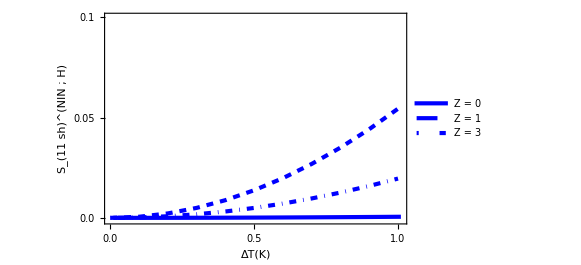

```mathematica
ListLinePlot[{data1hn,data2hn,data3hn},Frame->True,PlotRange->{-0.001,0.1},Frame->True,PlotLegends->Placed[{"Z = 0","Z = 1","Z = 3"},{Right,Top}],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Style["S_(11  sh)^(NIN ;  H)",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{0.05,"0.05"},{0.1,"0.1"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
Rshnh=Table[Flatten[{Import["check300.dat"][[x]][[1]],Import["check300.dat"][[x]][[10]]/Import["check300.dat"][[x]][[11]]}],{x,1,11,1}]
```

{{0.001,15.8019},{0.101,15.8019},{0.201,15.8019},{0.301,15.8019},{0.401,15.8019},{0.501,15.8019},{0.601,15.8019},{0.701,15.8019},{0.801,15.8019},{0.901,15.8019},{1.001,15.8019}}

```mathematica
Rshnh1=Table[Flatten[{Import["check301.dat"][[x]][[1]],Import["check301.dat"][[x]][[10]]/Import["check301.dat"][[x]][[11]]}],{x,1,11,1}]
Rshnh2=Table[Flatten[{Import["check302.dat"][[x]][[1]],Import["check302.dat"][[x]][[10]]/Import["check302.dat"][[x]][[11]]}],{x,1,11,1}]
```

{{0.001,1.58025},{0.101,1.58025},{0.201,1.58025},{0.301,1.58025},{0.401,1.58025},{0.501,1.58025},{0.601,1.58025},{0.701,1.58025},{0.801,1.58025},{0.901,1.58025},{1.001,1.58025}}

{{0.001,0.122774},{0.101,0.122774},{0.201,0.122774},{0.301,0.122774},{0.401,0.122774},{0.501,0.122774},{0.601,0.122774},{0.701,0.122774},{0.801,0.122774},{0.901,0.122774},{1.001,0.122774}}

```mathematica
ListLinePlot[{Rshnh,Rshnh1,Rshnh2},Frame->True,PlotRange->{-0.3,16.1},Frame->True,PlotLegends->Placed[{"Z=0","Z = 1","Z = 3"},{Right,Top}],FrameLabel->{Style["ΔT(K)",21,Bold,Black],Style["Q_(11  sh)^(NIS ;  H)/Q_(11  sh)^(NIN ;  H)",23,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{16,"16.0"},{8.0,"8.0"},{21.0,"21.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5, "0.5"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, DotDashed]},ImageSize->420,LabelStyle->Directive[Bold,Black,16]]
```